```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## Import Data

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
Vdata=SplitBy[Import["latticedata/AllData2p1Flavors/Vall.txt","Table"],First];

ReVdataT[n_]:=Table[Vdata[[n,x,2;;3]],{x,1,Dimensions[Vdata[[n]]][[1]]}];
ImVdataT[n_]:=Table[{Vdata[[n,x,2]],Vdata[[n,x,5]]},{x,1,Dimensions[Vdata[[n]]][[1]]}];
ReVdataTe[n_]:=Table[Vdata[[n,x,2;;4]],{x,1,Dimensions[Vdata[[n]]][[1]]}];
ImVdataTe[n_]:=Table[{Vdata[[n,x,2]],Vdata[[n,x,5]],Vdata[[n,x,6]]},{x,1,Dimensions[Vdata[[n]]][[1]]}];
ReVdataTn[n_]:=ReVdataT[n]/.{a_,b_}:>{a/0.197327,b};
ImVdataTn[n_]:=ImVdataT[n]/.{a_,b_}:>{a/0.197327,b};
ReVdataTne[n_]:=ReVdataTe[n]/.{a_,b_,c_}:>{a/0.197327,b,c};
ImVdataTne[n_]:=ImVdataTe[n]/.{a_,b_,c_}:>{a/0.197327,b,c};

T0data=Join[{Import["latticedata/LowTemp/OlafPotentialLinesTmax12PotentialT41.05.dat","Table"][[All,1;;3]]},{Import["latticedata/LowTemp/OlafPotentialLinesTmax12PotentialT71.54.dat","Table"][[All,1;;3]]}];
T0data=T0data/.{a_,b_,c_}:>{a/0.197327,b,c};
```

## Define functions for real part

```mathematica
ReV[r_,m_,α_,σ_,c_]:=-α m-α Exp[-m r]/r-Gamma[1/4]/(2^(3/4)√π)σ/((m^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(m^2 σ/α)^(1/4) r]+Gamma[1/4]/(2Gamma[3/4])σ/((m^2 σ/α)^(1/4))+c
ReVm0[r_,α_,σ_,c_,d_]:=c-α/r+σ r+d r^2;
```

## Low T Cornell Fitting & Interpolation

```mathematica
T0datarand[n_]:=Table[{T0data[[n]][[i,1]],RandomVariate[NormalDistribution[T0data[[n]][[i,2]],T0data[[n]][[i,3]]]]},{i,Length[T0data[[n]]]}]
```

### beta = 6.9 Fitting

```mathematica
VaryFitLow=Range[2,4];
VaryFitHigh=Range[20,28];
VaryFit=Flatten[Table[{VaryFitLow[[j]],VaryFitHigh[[i]]},{j,1,Length[VaryFitLow]},{i,1,Length[VaryFitHigh]}],1];

VaryFitLowAR={2,2,2,2,2,1,3,1,3}+1;
VaryFitHighAR={24,28,26,30,22,24,24,26,22}-2;
```

#### Varied Weights (not in use)

{0.449955,0.0207984}

{0.223087,0.00686867}

{1.75543,0.0257048}

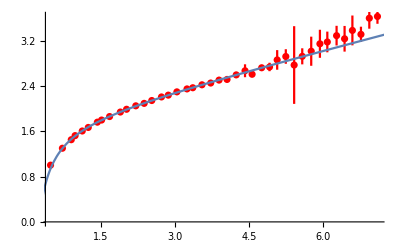

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

{0.437304,0.0639055}

{0.230147,0.0267482}

{1.7356,0.088547}

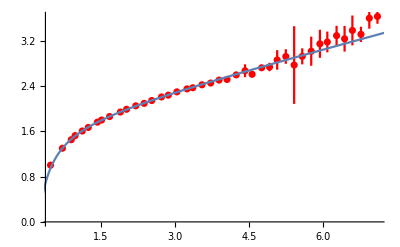

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]]),VarianceEstimatorFunction->(1&)];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

{0.449955,0.0207984}

{0.223087,0.00686867}

{1.75543,0.0257048}

-Graphics-

```mathematica
αfit69={};
σfit69={};
cfit69={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[1,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[1,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2,VarianceEstimatorFunction->(1&)];
αfit69=Append[αfit69,al/.fit["BestFitParameters"]];
σfit69=Append[σfit69,sig/.fit["BestFitParameters"]];
cfit69=Append[cfit69,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal69={Mean[αfit69],StandardDeviation[αfit69]}
σfinal69={Mean[σfit69],StandardDeviation[σfit69]}
cfinal69={Mean[cfit69],StandardDeviation[cfit69]}
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69[[1]],σfinal69[[1]],cfinal69[[1]]],{r,0,10}]}]
```

{0.437304,0.0639055}

{0.230147,0.0267482}

{1.7356,0.088547}

-Graphics-

#### Use this one!

```mathematica
αfit69r={};
σfit69r={};
cfit69r={};
dfit69r={};
SetSharedVariable[αfit69r,σfit69r,cfit69r,dfit69r];
ParallelDo[Module[{fit},fit=NonlinearModelFit[T0datarand[1][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const,const1],{al,sig,const,const1},r];
αfit69r=Append[αfit69r,al/.fit["BestFitParameters"]];
σfit69r=Append[σfit69r,sig/.fit["BestFitParameters"]];
cfit69r=Append[cfit69r,const/.fit["BestFitParameters"]];
dfit69r=Append[dfit69r,const1/.fit["BestFitParameters"]];];,{ii,1,100},{i,1,Length[VaryFit]}]
αfinal69r={Mean[αfit69r],StandardDeviation[αfit69r]}
σfinal69r={Mean[σfit69r],StandardDeviation[σfit69r]}
cfinal69r={Mean[cfit69r],StandardDeviation[cfit69r]}
dfinal69r={Mean[dfit69r],StandardDeviation[dfit69r]}
```

{0.406431,0.109021}

{0.272259,0.101689}

{1.67039,0.192393}

{-0.00822125,0.0161256}

```mathematica
αfinal69r={0.4710512623279609,0.04708158386118884}(*run with 10k points, all varied fitting*)
```

{0.471051,0.0470816}

```mathematica
σfinal69r={0.21706712111822668,0.015928132568206174}
```

{0.217067,0.0159281}

```mathematica
cfinal69r={1.7808043891992207,0.059392193900140486}
```

{1.7808,0.0593922}

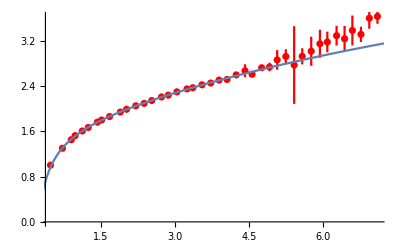

```mathematica
Show[{ErrorListPlot[T0data[[1,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal69r[[1]],σfinal69r[[1]],cfinal69r[[1]],dfinal69r[[1]]],{r,0,10}]}]
```

### beta = 7.4 Fitting

```mathematica
VaryFitLow=Range[5,7];
VaryFitHigh=Range[26,34];
VaryFit=Flatten[Table[{VaryFitLow[[j]],VaryFitHigh[[i]]},{j,1,Length[VaryFitLow]},{i,1,Length[VaryFitHigh]}],1];
```

```mathematica
VaryFitLowAR={2,2,2,2,2,1,3,1,3}+4;
VaryFitHighAR={24,28,26,30,22,24,24,26,22}+4;
```

#### Varied Weights (not in use)

{0.386026,0.00681763}

{0.264172,0.003189}

{2.65021,0.00972345}

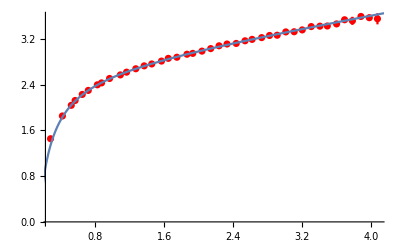

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

{0.389033,0.00967473}

{0.263519,0.00430806}

{2.65451,0.0135868}

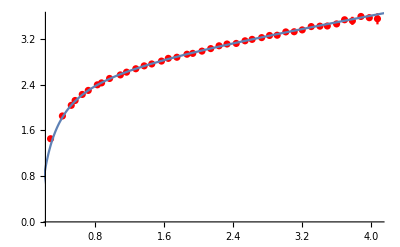

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]]),VarianceEstimatorFunction->(1&)];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

{0.386026,0.00681763}

{0.264172,0.003189}

{2.65021,0.00972345}

-Graphics-

```mathematica
αfit748={};
σfit748={};
cfit748={};
Do[Module[{fit},fit=NonlinearModelFit[T0data[[2,All,1;;2]][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const],{al,sig,const},r,Weights->1/(T0data[[2,All,3]][[VaryFit[[i,1]];;VaryFit[[i,2]]]])^2,VarianceEstimatorFunction->(1&)];
αfit748=Append[αfit748,al/.fit["BestFitParameters"]];
σfit748=Append[σfit748,sig/.fit["BestFitParameters"]];
cfit748=Append[cfit748,const/.fit["BestFitParameters"]]];,{i,1,Length[VaryFit]}]
αfinal748={Mean[αfit748],StandardDeviation[αfit748]}
σfinal748={Mean[σfit748],StandardDeviation[σfit748]}
cfinal748={Mean[cfit748],StandardDeviation[cfit748]}
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748[[1]],σfinal748[[1]],cfinal748[[1]]],{r,0,10}]}]
```

{0.389033,0.00967473}

{0.263519,0.00430806}

{2.65451,0.0135868}

-Graphics-

#### Use this one!

```mathematica
αfit748r={};
σfit748r={};
cfit748r={};
dfit748r={};
SetSharedVariable[αfit748r,σfit748r,cfit748r,dfit748r];
ParallelDo[Module[{fit},fit=NonlinearModelFit[T0datarand[2][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReVm0[r,al,sig,const,const1],{al,sig,const,const1},r];
αfit748r=Append[αfit748r,al/.fit["BestFitParameters"]];
σfit748r=Append[σfit748r,sig/.fit["BestFitParameters"]];
cfit748r=Append[cfit748r,const/.fit["BestFitParameters"]];
dfit748r=Append[dfit748r,const1/.fit["BestFitParameters"]];];,{ii,1,100},{i,1,Length[VaryFit]}]
αfinal748r={Mean[αfit748r],StandardDeviation[αfit748r]}
σfinal748r={Mean[σfit748r],StandardDeviation[σfit748r]}
cfinal748r={Mean[cfit748r],StandardDeviation[cfit748r]}
dfinal748r={Mean[dfit748r],StandardDeviation[dfit748r]}
```

{0.369525,0.0350224}

{0.279673,0.0953392}

{2.61925,0.105111}

{-0.00229709,0.0263186}

```mathematica
αfinal748r={0.38421689745948295,0.026725063814154956} (*run with 10k points, all varied fitting*)
```

{0.384217,0.0267251}

```mathematica
σfinal748r={0.26496110508771914,0.014291026549795801}
```

{0.264961,0.014291}

```mathematica
cfinal748r={2.646969377008623,0.041757844174975016}
```

{2.64697,0.0417578}

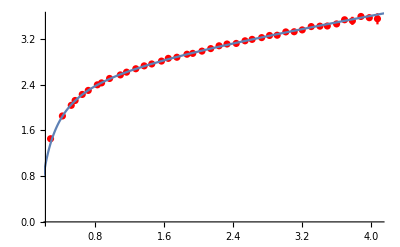

```mathematica
Show[{ErrorListPlot[T0data[[2,All]],PlotStyle->{Red},PlotRange->All],Plot[ReVm0[r,αfinal748r[[1]],σfinal748r[[1]],cfinal748r[[1]],dfinal748r[[1]]],{r,0,10}]}]
```

### Linear Interpolation

```mathematica
β={6.8,6.9,7,7.125,7.25,7.3,7.48};
T={0.1478,0.1642,0.1818,0.2054,0.2317,0.2425,0.2861};
```

```mathematica
btinter=Interpolation[Transpose[{T,β}]];
btinter1=Interpolation[Transpose[{T,β}],InterpolationOrder->1];
```

```mathematica
beta2T0res={αfinal69r,σfinal69r,cfinal69r};
beta7T0res={αfinal748r,σfinal748r,cfinal748r};
```

```mathematica
T0constfit={LinearModelFit[{{β[[2]],beta2T0res[[1,1]]},{β[[7]],beta7T0res[[1,1]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[2,1]]},{β[[7]],beta7T0res[[2,1]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[3,1]]},{β[[7]],beta7T0res[[3,1]]}},x,x]};
T0errfit={LinearModelFit[{{β[[2]],beta2T0res[[1,2]]},{β[[7]],beta7T0res[[1,2]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[2,2]]},{β[[7]],beta7T0res[[2,2]]}},x,x],LinearModelFit[{{β[[2]],beta2T0res[[3,2]]},{β[[7]],beta7T0res[[3,2]]}},x,x]};
```

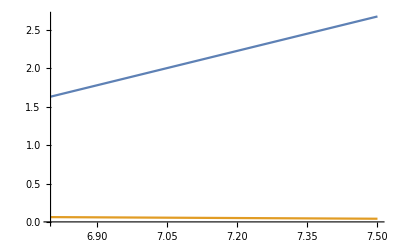

```mathematica
Plot[{T0constfit[[3]][x],T0errfit[[3]][x]},{x,6.8,7.5}]
```

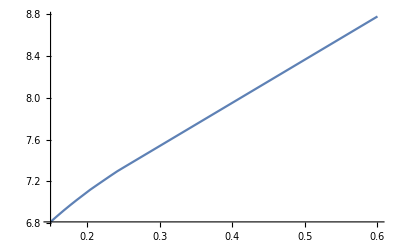

```mathematica
Plot[btinter1[x],{x,0.15,0.6}]
```

```mathematica
Table[T0constfit[[2]][β[[i]]],{i,1,Length[β]}]
```

{0.20881,0.217067,0.225325,0.235647,0.245969,0.250097,0.264961}

```mathematica
Table[T0errfit[[2]][β[[i]]],{i,1,Length[β]}]
```

{0.0162104,0.0159281,0.0156459,0.015293,0.0149402,0.0147991,0.014291}

```mathematica
Tscanc=Table[i,{i,0.15,0.25,0.003}]
```

{0.15,0.153,0.156,0.159,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195,0.198,0.201,0.204,0.207,0.21,0.213,0.216,0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249}

```mathematica
Tscanb=Table[i,{i,0.15,0.6,0.005}]
```

{0.15,0.155,0.16,0.165,0.17,0.175,0.18,0.185,0.19,0.195,0.2,0.205,0.21,0.215,0.22,0.225,0.23,0.235,0.24,0.245,0.25,0.255,0.26,0.265,0.27,0.275,0.28,0.285,0.29,0.295,0.3,0.305,0.31,0.315,0.32,0.325,0.33,0.335,0.34,0.345,0.35,0.355,0.36,0.365,0.37,0.375,0.38,0.385,0.39,0.395,0.4,0.405,0.41,0.415,0.42,0.425,0.43,0.435,0.44,0.445,0.45,0.455,0.46,0.465,0.47,0.475,0.48,0.485,0.49,0.495,0.5,0.505,0.51,0.515,0.52,0.525,0.53,0.535,0.54,0.545,0.55,0.555,0.56,0.565,0.57,0.575,0.58,0.585,0.59,0.595,0.6}

```mathematica
βTscanc=Table[btinter[i],{i,0.15,0.25,0.003}]
```

{6.81385,6.8325,6.85091,6.86907,6.887,6.9047,6.92218,6.93945,6.95652,6.97339,6.99007,7.00662,7.02305,7.03931,7.05539,7.0713,7.08702,7.10256,7.1179,7.13291,7.1476,7.16212,7.17648,7.19072,7.20484,7.21888,7.23284,7.24676,7.26075,7.2747,7.28855,7.30228,7.31589,7.32936}

```mathematica
βTscanc1=Table[btinter1[i],{i,0.15,0.25,0.003}]
```

{6.81341,6.83171,6.85,6.86829,6.88659,6.90455,6.92159,6.93864,6.95568,6.97273,6.98977,7.00636,7.02225,7.03814,7.05403,7.06992,7.08581,7.10169,7.11758,7.1326,7.14686,7.16112,7.17538,7.18964,7.2039,7.21816,7.23241,7.24667,7.26065,7.27454,7.28843,7.30206,7.31445,7.32683}

```mathematica
βTscanb=Join[Table[btinter[i],{i,0.15,0.285,0.005}],Table[btinter1[i],{i,0.29,0.6,0.005}]]
```

InterpolatingFunction::dmval: Input value {0.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.295} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{6.81385,6.8448,6.87507,6.9047,6.93372,6.96216,6.99007,7.01759,7.04469,7.0713,7.0974,7.12298,7.1476,7.17171,7.19544,7.21888,7.24212,7.26541,7.28855,7.31137,7.33382,7.35585,7.3774,7.39842,7.41885,7.43864,7.45773,7.47607,7.4961,7.51674,7.53739,7.55803,7.57867,7.59931,7.61995,7.6406,7.66124,7.68188,7.70252,7.72317,7.74381,7.76445,7.78509,7.80573,7.82638,7.84702,7.86766,7.8883,7.90894,7.92959,7.95023,7.97087,7.99151,8.01216,8.0328,8.05344,8.07408,8.09472,8.11537,8.13601,8.15665,8.17729,8.19794,8.21858,8.23922,8.25986,8.2805,8.30115,8.32179,8.34243,8.36307,8.38372,8.40436,8.425,8.44564,8.46628,8.48693,8.50757,8.52821,8.54885,8.5695,8.59014,8.61078,8.63142,8.65206,8.67271,8.69335,8.71399,8.73463,8.75528,8.77592}

```mathematica
βTscanb1=Table[btinter1[i],{i,0.15,0.6,0.005}]
```

InterpolatingFunction::dmval: Input value {0.29} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.295} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{6.81341,6.8439,6.87439,6.90455,6.93295,6.96136,6.98977,7.01695,7.04343,7.06992,7.0964,7.12288,7.14686,7.17063,7.19439,7.21816,7.24192,7.26528,7.28843,7.31032,7.33096,7.35161,7.37225,7.39289,7.41353,7.43417,7.45482,7.47546,7.4961,7.51674,7.53739,7.55803,7.57867,7.59931,7.61995,7.6406,7.66124,7.68188,7.70252,7.72317,7.74381,7.76445,7.78509,7.80573,7.82638,7.84702,7.86766,7.8883,7.90894,7.92959,7.95023,7.97087,7.99151,8.01216,8.0328,8.05344,8.07408,8.09472,8.11537,8.13601,8.15665,8.17729,8.19794,8.21858,8.23922,8.25986,8.2805,8.30115,8.32179,8.34243,8.36307,8.38372,8.40436,8.425,8.44564,8.46628,8.48693,8.50757,8.52821,8.54885,8.5695,8.59014,8.61078,8.63142,8.65206,8.67271,8.69335,8.71399,8.73463,8.75528,8.77592}

```mathematica
Table[T0constfit[[2]][βTscanc[[i]]],{i,1,Length[βTscanc]}]
```

{0.209953,0.211494,0.213013,0.214513,0.215993,0.217455,0.218899,0.220325,0.221734,0.223127,0.224505,0.225871,0.227228,0.22857,0.229899,0.231212,0.23251,0.233793,0.235061,0.2363,0.237513,0.238712,0.239898,0.241073,0.24224,0.243399,0.244552,0.245701,0.246857,0.248008,0.249152,0.250286,0.25141,0.252522}

```mathematica
Table[T0constfit[[1]][βTscanc[[i]]],{i,1,Length[βTscanc]}]
```

{0.48395,0.481156,0.478401,0.475682,0.472998,0.470348,0.467731,0.465145,0.46259,0.460064,0.457566,0.455089,0.452629,0.450195,0.447787,0.445406,0.443052,0.440726,0.438428,0.436181,0.433982,0.431809,0.429658,0.427526,0.425412,0.42331,0.42122,0.419137,0.417041,0.414953,0.41288,0.410824,0.408787,0.40677}

```mathematica
Table[T0constfit[[3]][βTscanc[[i]]],{i,1,Length[βTscanc]}]
```

{1.65214,1.68001,1.70749,1.73462,1.76139,1.78782,1.81393,1.83972,1.86521,1.8904,1.91532,1.94003,1.96456,1.98884,2.01286,2.03662,2.0601,2.0833,2.10622,2.12863,2.15057,2.17225,2.1937,2.21496,2.23605,2.25701,2.27787,2.29865,2.31955,2.34038,2.36106,2.38157,2.40189,2.42201}

```mathematica
Table[T0constfit[[2]][βTscanb[[i]]],{i,1,Length[βTscanb]}]
```

{0.209953,0.212509,0.215009,0.217455,0.219851,0.2222,0.224505,0.226777,0.229015,0.231212,0.233367,0.23548,0.237513,0.239504,0.241463,0.243399,0.245318,0.247241,0.249152,0.251036,0.25289,0.254709,0.256489,0.258224,0.259912,0.261546,0.263122,0.264637,0.266291,0.267995,0.2697,0.271404,0.273109,0.274813,0.276518,0.278222,0.279927,0.281632,0.283336,0.285041,0.286745,0.28845,0.290154,0.291859,0.293563,0.295268,0.296972,0.298677,0.300382,0.302086,0.303791,0.305495,0.3072,0.308904,0.310609,0.312313,0.314018,0.315723,0.317427,0.319132,0.320836,0.322541,0.324245,0.32595,0.327654,0.329359,0.331063,0.332768,0.334473,0.336177,0.337882,0.339586,0.341291,0.342995,0.3447,0.346404,0.348109,0.349813,0.351518,0.353223,0.354927,0.356632,0.358336,0.360041,0.361745,0.36345,0.365154,0.366859,0.368563,0.370268,0.371973}

```mathematica
Table[T0constfit[[1]][βTscanb[[i]]],{i,1,Length[βTscanb]}]
```

{0.48395,0.479315,0.474783,0.470348,0.466004,0.461745,0.457566,0.453446,0.449389,0.445406,0.441498,0.437668,0.433982,0.430372,0.42682,0.42331,0.41983,0.416344,0.41288,0.409464,0.406102,0.402804,0.399578,0.396431,0.393372,0.390409,0.387551,0.384805,0.381806,0.378716,0.375625,0.372535,0.369445,0.366354,0.363264,0.360173,0.357083,0.353992,0.350902,0.347812,0.344721,0.341631,0.33854,0.33545,0.332359,0.329269,0.326179,0.323088,0.319998,0.316907,0.313817,0.310726,0.307636,0.304545,0.301455,0.298365,0.295274,0.292184,0.289093,0.286003,0.282912,0.279822,0.276732,0.273641,0.270551,0.26746,0.26437,0.261279,0.258189,0.255099,0.252008,0.248918,0.245827,0.242737,0.239646,0.236556,0.233465,0.230375,0.227285,0.224194,0.221104,0.218013,0.214923,0.211832,0.208742,0.205652,0.202561,0.199471,0.19638,0.19329,0.190199}

```mathematica
Table[T0constfit[[3]][βTscanb[[i]]],{i,1,Length[βTscanb]}]
```

{1.65214,1.69837,1.74358,1.78782,1.83115,1.87364,1.91532,1.95641,1.99688,2.03662,2.0756,2.1138,2.15057,2.18657,2.22201,2.25701,2.29173,2.32651,2.36106,2.39514,2.42867,2.46156,2.49375,2.52514,2.55565,2.5852,2.61371,2.6411,2.67101,2.70184,2.73267,2.76349,2.79432,2.82515,2.85598,2.8868,2.91763,2.94846,2.97928,3.01011,3.04094,3.07176,3.10259,3.13342,3.16424,3.19507,3.2259,3.25672,3.28755,3.31838,3.3492,3.38003,3.41086,3.44168,3.47251,3.50334,3.53417,3.56499,3.59582,3.62665,3.65747,3.6883,3.71913,3.74995,3.78078,3.81161,3.84243,3.87326,3.90409,3.93491,3.96574,3.99657,4.02739,4.05822,4.08905,4.11987,4.1507,4.18153,4.21236,4.24318,4.27401,4.30484,4.33566,4.36649,4.39732,4.42814,4.45897,4.4898,4.52062,4.55145,4.58228}

## Debye Fitting

```mathematica
ReVdataTnrand[n_]:=Table[{ReVdataTne[n][[i,1]],RandomVariate[NormalDistribution[ReVdataTne[n][[i,2]],ReVdataTne[n][[i,3]]]]},{i,Length[ReVdataTne[n]]}]
```

```mathematica
T0constrand[n_]:={RandomVariate[NormalDistribution[T0constfit[[1]][β[[n]]],T0errfit[[1]][β[[n]]]]],RandomVariate[NormalDistribution[T0constfit[[2]][β[[n]]],T0errfit[[2]][β[[n]]]]],RandomVariate[NormalDistribution[T0constfit[[3]][β[[n]]],T0errfit[[3]][β[[n]]]]]}
```

```mathematica
VaryFitLow=Range[1,3];
VaryFitHigh=Range[18,30];
VaryFit=Flatten[Table[{VaryFitLow[[j]],VaryFitHigh[[i]]},{j,1,Length[VaryFitLow]},{i,1,Length[VaryFitHigh]}],1];
VaryFitLow={2,2,2,2,2,1,3,1,3};
VaryFitHigh={32,28,26,24,20,22,22,30,30}-2;
```

```mathematica
fitrandall[n_]:=ParallelTable[Quiet[m/.NonlinearModelFit[ReVdataTnrand[n][[VaryFit[[i,1]];;VaryFit[[i,2]]]],ReV[r,m,T0constrand[n][[1]],T0constrand[n][[2]],T0constrand[n][[3]]],{{m,0.1}},r]["BestFitParameters"]],{ii,1,10000},{i,1,Length[VaryFit]}];
mdfitrandres=ConstantArray[0,Length[Vdata]];
mdfitrandfinal=ConstantArray[0,Length[Vdata]];
```

```mathematica
Do[mdfitrandres[[n]]=fitrandall[n];
mdfitrandfinal[[n]]={Mean[Flatten[mdfitrandres[[n]]]],StandardDeviation[Flatten[mdfitrandres[[n]]]]};
Print[mdfitrandfinal[[n]]],{n,Length[mdfitrandres]}]//AbsoluteTiming
```

{20999.3,Null}

```mathematica
mdfitrandfinal={{0.038919565918040445,0.06743682653727344},{0.12582094383686163,0.10923208048614581},{0.1892583277055926,0.12852782269560006},{0.30988003094936495,0.18358091276753688},{0.48025965960625705,0.1479696311077649},{0.49657169002278573,0.1791783591997105},{0.6465066249674667,0.1798587912586749}}(*10k run*)
```

{{0.0389196,0.0674368},{0.125821,0.109232},{0.189258,0.128528},{0.30988,0.183581},{0.48026,0.14797},{0.496572,0.179178},{0.646507,0.179859}}

```mathematica
Manipulate[Show[{Plot[{ReV[r,mdfitrandfinal[[n,1]],T0constfit[[1]][β[[n]]],T0constfit[[2]][β[[n]]],T0constfit[[3]][β[[n]]]],ReV[r,mdfitrandfinal[[n,1]]+mdfitrandfinal[[n,2]],T0constfit[[1]][β[[n]]],T0constfit[[2]][β[[n]]],T0constfit[[3]][β[[n]]]],ReV[r,If[mdfitrandfinal[[n,1]]-mdfitrandfinal[[n,2]]>0,mdfitrandfinal[[n,1]]-mdfitrandfinal[[n,2]],0.0000000001],T0constfit[[1]][β[[n]]],T0constfit[[2]][β[[n]]],T0constfit[[3]][β[[n]]]]},{r,0,10}],ErrorListPlot[ReVdataTne[n],PlotRange->All,PlotStyle->{Red}]}],{n,1,Length[mdfitrandfinal],1}]
```

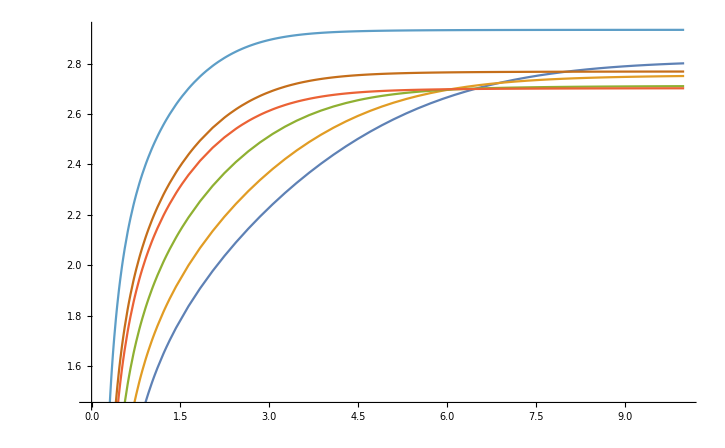

```mathematica
Plot[{ReV[r,mdfitrandfinal[[2,1]],T0constfit[[1]][β[[2]]],T0constfit[[2]][β[[2]]],T0constfit[[3]][β[[2]]]],ReV[r,mdfitrandfinal[[3,1]],T0constfit[[1]][β[[3]]],T0constfit[[2]][β[[3]]],T0constfit[[3]][β[[3]]]],ReV[r,mdfitrandfinal[[4,1]],T0constfit[[1]][β[[4]]],T0constfit[[2]][β[[4]]],T0constfit[[3]][β[[4]]]],ReV[r,mdfitrandfinal[[5,1]],T0constfit[[1]][β[[5]]],T0constfit[[2]][β[[5]]],T0constfit[[3]][β[[5]]]],,ReV[r,mdfitrandfinal[[6,1]],T0constfit[[1]][β[[6]]],T0constfit[[2]][β[[6]]],T0constfit[[3]][β[[6]]]],ReV[r,mdfitrandfinal[[7,1]],T0constfit[[1]][β[[7]]],T0constfit[[2]][β[[7]]],T0constfit[[3]][β[[7]]]]},{r,0,10}]
```

```mathematica
mdfitAR={0.006612808256711139,0.11838248788551524,0.1870803288935863,0.26288830333533697,0.4797079970797252,0.4971567199527494,0.6554067022426473};
```

```mathematica
beta2T0resAR={0.455646041418761,0.22196921018206223,1.760305640923639};
beta7T0resAR={0.3855295399168057,0.2646854571686481,2.647963550234381};
```

```mathematica
T0constfitAR={LinearModelFit[{{β[[2]],beta2T0resAR[[1]]},{β[[7]],beta7T0resAR[[1]]}},x,x],LinearModelFit[{{β[[2]],beta2T0resAR[[2]]},{β[[7]],beta7T0resAR[[2]]}},x,x],LinearModelFit[{{β[[2]],beta2T0resAR[[3]]},{β[[7]],beta7T0resAR[[3]]}},x,x]};
```

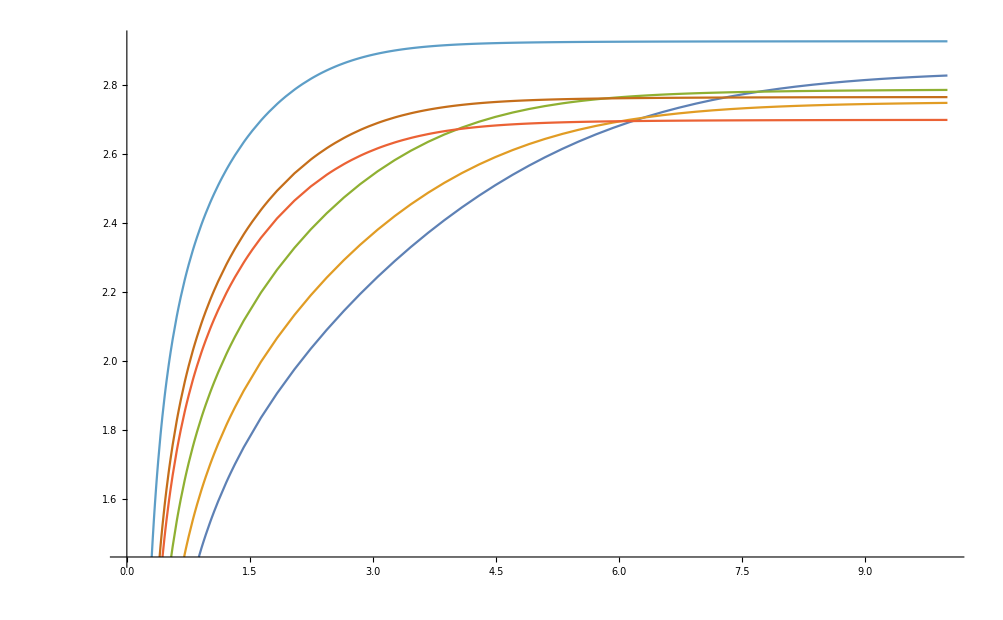

```mathematica
Plot[{ReV[r,mdfitAR[[2]],T0constfitAR[[1]][β[[2]]],T0constfitAR[[2]][β[[2]]],T0constfitAR[[3]][β[[2]]]],ReV[r,mdfitAR[[3]],T0constfitAR[[1]][β[[3]]],T0constfitAR[[2]][β[[3]]],T0constfitAR[[3]][β[[3]]]],ReV[r,mdfitAR[[4]],T0constfitAR[[1]][β[[4]]],T0constfitAR[[2]][β[[4]]],T0constfitAR[[3]][β[[4]]]],ReV[r,mdfitAR[[5]],T0constfitAR[[1]][β[[5]]],T0constfitAR[[2]][β[[5]]],T0constfitAR[[3]][β[[5]]]],,ReV[r,mdfitAR[[6]],T0constfitAR[[1]][β[[6]]],T0constfitAR[[2]][β[[6]]],T0constfitAR[[3]][β[[6]]]],ReV[r,mdfitAR[[7]],T0constfitAR[[1]][β[[7]]],T0constfitAR[[2]][β[[7]]],T0constfitAR[[3]][β[[7]]]]},{r,0,10}]
```

## Plotting of imaginary part

```mathematica
g[x_]:=Quiet[2NIntegrate[p/(p^2+1)Sinc[p x],{p,0,∞}]];
ϕ[x_]:=Quiet[2NIntegrate[z/((z^2+1)^2)Sinc[x z],{z,0,∞}]];
```

```mathematica
ϵ=1/1000;
ϕ1table10=Quiet[ Join[Parallelize[Table[{x,1-ϕ[x]},{x,ϵ/100,2,10ϵ}]],Parallelize[Table[{x,1-ϕ[x]},{x,2+100ϵ,10,100ϵ}]]]];
ϕ110=Interpolation[ϕ1table10];
```

```mathematica
Do[
Module[{σ=T0constfit[[2]][β[[n]]], α=T0constfit[[1]][β[[n]]],mD=mdfitrandfinal[[n,1]],c,r,μ},
μ=(mD^2 σ/α)^(1/4);
r=mD/μ;
pg=1;
c=Re[ParabolicCylinderD[-1/2,ⅈ ϵ/100]NIntegrate[ParabolicCylinderD[-1/2,√2 x] x^2 g[x r],{x,0,∞}]];
ψ1[x_,r_]:=c-ParabolicCylinderD[-1/2,√2 x]NIntegrate[y^2 g[y r]Re[ParabolicCylinderD[-1/2,ⅈ √2 y]],{y,0,x},PrecisionGoal->pg]-Re[ParabolicCylinderD[-1/2,ⅈ √2 x]]NIntegrate[ParabolicCylinderD[-1/2,√2 y] y^2 g[y r],{y,x,∞},PrecisionGoal->pg];
ψ1table10[n]=Join[Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,ϵ/100,1,10ϵ}]],Parallelize[Table[{x,Quiet[ψ1[x,r]]},{x,1+100ϵ,10+ϵ,100ϵ}]]];],{n,1,Length[Vdata]}]
```

$Aborted

```mathematica
ImV[x_,n_]:=T0constfit[[1]][β[[n]]] T[[n]] ϕ110[mdfitrandfinal[[n,1]] x]+T0constfit[[1]][β[[n]]] T[[n]] Interpolation[ψ1table10[n]][(mdfitrandfinal[[n,1]]^2(T0constfit[[2]][β[[n]]])/(T0constfit[[1]][β[[n]]]))^(1/4) x];
```

```mathematica
(*Manipulate[Show[Plot[{ImV[x,n],ImVar[x,n]},{x,0,10}],ErrorListPlot[ImVdataTne[n]],PlotRange->All],{n,1,Length[ReVdata],1}]*)
```